# DMDGP Package

## Instance Creation

### Source Code

```mathematica
SetPositionUsingBasicOperations::usage="Set the atoms positions using atomic rotations and translations.";SetPositionUsingBasicOperations[d_,t_,w_]:=
Module[
(* declare local variables *)
{a,b,c,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X=ReplacePart[X,{1->{0,0,0},2->{-d[[2]],0,0}, 3->{-d[[2]]+d[[3]]Cos[t[[3]]],d[[3]]Sin[t[[3]]] ,0}}];
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[t[[i]],n];
v=R[v];
(* apply torsion rotation and translation *)
R=RotationTransform[w[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X=ReplacePart[X,i->v]
];
X
];

SetPositionUsingTransformationMatrices::usage="Set the atoms positions using internal coordinate system.";
SetPositionUsingTransformationMatrices[d_,t_,w_]:=
Module[
{B,B1,B2,B3,X,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X=ReplacePart[X,{1->{0,0,0},2->{-d[[2]],0,0}, 3->{-d[[2]]+d[[3]]Cos[t[[3]]],d[[3]]Sin[t[[3]]] ,0}}];
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
{ct,st}={Cos[t[[3]]],Sin[t[[3]]]};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[t[[i]]],Sin[t[[i]]]};
{cw,sw}={Cos[w[[i]]],Sin[w[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X=ReplacePart[X,i->v[[{1,2,3}]]];
];
X
];

GenerateRandom3DBackbone::usage="Generates a random backbone in tridimensional Euclidean space.";
GenerateRandom3DBackbone[numberOfAtoms_]:=
Module[
(* declare the local variables *)
{d,t,w,X,output},
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d=ReplacePart[d,1->0];
(* plane angles *)
t=Table[1.91,{i,numberOfAtoms}];
t=ReplacePart[t,{1->0,2->0}];
(* torsion angles *)
w=Table[RandomReal[2Pi],{i,numberOfAtoms}];
w=ReplacePart[w,{1->0,2->0,3->0}];
(* set the remaining 3d positions *)
(* X=SetPositionUsingBasicOperations[d,t,w]; *)
X=SetPositionUsingTransformationMatrices[d,t,w];
(* set output *)
<|"Points"->X,"TorsionAngles"->w,"CovalentBondLengths"->d,"PlaneRotationAngles"->t|>
];

GetMatrixDistance::usage="Gets the complete distance matrix for all coordinates in the array X.";
GetMatrixDistance[x_]:=Table[Norm[x[[i]]-x[[j]]],{i,1,Length[x]},{j,1,Length[x]}];

GenerateRandomDMDGPInstance::usage="Generates a random DMDGP instance.";
GenerateRandomDMDGPInstance[numberOfAtoms_]:=
Module[
(* declare local variables *)
{i,j,X,G,D,output,dij},
X=GenerateRandom3DBackbone[numberOfAtoms];
D=GetMatrixDistance[X["Points"]];
G=Table[If[And[0<D[[i]][[j]],D[[i]][[j]]≤5],D[[i]][[j]],Infinity],{i,1,numberOfAtoms},{j,1,numberOfAtoms}];
G=WeightedAdjacencyGraph[G];
(* set output *)
<|"X"->X,"G"->G|>
];

Plot3DBackbone::usage="Plots the points using the coordinates of X[Points].";
Plot3DBackbone[X_]:=Graphics3D[{Line[X["Points"]],{PointSize[Large],Blue,Point[X["Points"]]}}, Axes->True]

CalculateProteinAngles::usage="Calculates the protein angles (plane and torsion) considering the sequence A-B-C-D.";
CalculateProteinAngles[A_,B_,C_,D_]:=
Module[
(* Calculate the plane and torsion angles for X4 *)
{nabc, nbcd},
(* centered at C *)
Print["Angle[BCD] =",N[VectorAngle[B-C,D-C]]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
Print["Angle[ABCD]=",N[VectorAngle[nabc,nbcd]]];
];

CalculateProteinAnglesForAtomAtPosition::usage="Calculates the protein angles (plane and torsion) to i-th atom.";
CalculateProteinAnglesForAtomAtPosition[X_,i_]:=CalculateProteinAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];
```

### Examples

#### Generating Random Backbone

```mathematica
X=GenerateRandom3DBackbone[7];
Print["X=",X];
Plot3DBackbone[X]
```

X=<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-3.55135,1.44201,0.159936},{-4.20697,1.3445,-1.21459},{-5.62371,0.797908,-1.06377},{-6.49052,1.82607,-0.342528}},TorsionAngles→{0,0,0,3.25296,4.7439,2.75079,1.18401},CovalentBondLengths→{0,1.526,1.526,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91,1.91,1.91}|>

-Graphics3D-

#### Set Position Using Different Coordinate Systems

```mathematica
d=X["CovalentBondLengths"];
t=X["PlaneRotationAngles"];
w=X["TorsionAngles"];
S=SetPositionUsingBasicOperations[d,t,w];
P=SetPositionUsingTransformationMatrices[d,t,w];
Print["S=",S];
Print["P=",P];
CalculateProteinAnglesForAtomAtPosition[S,7];
CalculateProteinAnglesForAtomAtPosition[P,7];
```

S={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-3.55135,1.44201,0.159936},{-4.20697,1.3445,-1.21459},{-5.62371,0.797908,-1.06377},{-6.49052,1.82607,-0.342528}}

P={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-3.55135,1.44201,0.159936},{-4.20697,1.3445,-1.21459},{-5.62371,0.797908,-1.06377},{-6.49052,1.82607,-0.342528}}

Angle[BCD] =1.91

Angle[ABCD]=1.18401

Angle[BCD] =1.91

Angle[ABCD]=1.18401

#### Generate Random DMDGP Instance

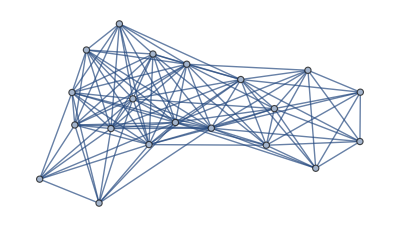

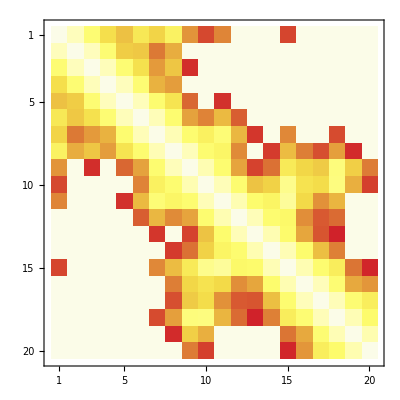

-Graphics3D-

```mathematica
M=GenerateRandomDMDGPInstance[20];
M["G"]
MatrixPlot[WeightedAdjacencyMatrix[M["G"]],ColorFunction->"TemperatureMap"]
Plot3DBackbone[M["X"]]
```

## MDGP Solvers

### Source Code

```mathematica
GetEdgeWeight::usage="Gets edge weight.";
GetEdgeWeight[G_,E_]:=Module[
{i,D={}},
If[Length[E[[1]]]>0,
(* E is a list of edges *)
For[i=1,i<Length[E],i++,AppendTo[D,PropertyValue[{G,e[[i]]},EdgeWeight]]],
(* E is a single edge *)
D=PropertyValue[{G,E},EdgeWeight]
];
D
];

IsPositionValid[G_,X_,i_]:=
Module[
(* local variables *)
{j,k,E,Xi,Xj,dij,Dij,tolerance=0.001,valid=True},
(* current position *)
Xi=X[[i]];
(* edges containing vertex i *)
E = EdgeList[G,i<->_];
For[k=1,k≤Length[E],k++,
(* neighbor index *)
j=E[[k]][[2]]; 
(* check only the distances to the precedent atoms *)
If[j>i,Continue[]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
dij=EuclideanDistance[Xi,Xj];
(* prescribed distance *)
Dij=GetEdgeWeight[G,E[[k]]];
(* check if actual distance is valid *)
If[Abs[Dij-dij]≥tolerance,valid=False;Break[]];
];
valid
];

CheckNaturalOrder[G_]:=Module[
{i,j},
For[i=4,i≤Length[G],i++,
For[j=1,j≤3,j++,
If[FailureQ[GetEdgeWeight[G,i<->(i-j)]],Throw["InvalidOrder"]];
];
];
];

BPTree[numberOfAtoms_]:=Module[
(* local variables *)
{branch},
(* init branch array *)
branch=Table[0,{i,numberOfAtoms}];
branch=ReplacePart[branch,{1->1,2->1,3->1}];
<|"Branch"->branch,"Node"->3,"HasNext"->True,"Pruned"->False|>
];

BPTreeHasNext[tree_]:=AnyTrue[tree["Branch"],#==0&];

For[i=1,i<Length[tree[
BPTreeGoToNext[tree_]:=
Module[
{i,j,B},
B=tree["Branch"];
i=tree["Node"];
If[tree["Pruned"] || i==Length[B],
(* if pruned or last node, search for a node to branch *)
While[i>0,If[B[[i]]==0,B[[i]]=1;Break[]];i--];
(* reset lower (until k) tree levels *)
For[j=i+1,j≤tree["Node"],B[j]=0],
(* if not pruned nor last node, just go to the child node *)
i++
];
<|"Branch"->B,"Node"->i,"HasNext"->True,"Pruned"->False|>
];

BPTreePrune[tree_]:=tree["Pruned"]=True;
SetAttributes[BPTreePrune,HoldFirst];

BPTreeGetNodePosition[tree_,G_,X_]:=Module[
{branch,i,a,b,c,dAD,dBD,dCD},
i=tree["Node"];
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
{dAD,dBD,dCD}=GetEdgeWeight[G,{i<->(i-3),i<->(i-2),i<->(i-1)}];
branch=tree["Branch"][[i]];
If[branch==0,
(* set branch-0 *)
Return[{,,}],
(* set branch-1 *)
Return[{,,}]
];
];
```

```mathematica
BP[G_]:=Module[
(* local variables *)
{i,j,k,t,dAB,dAC,dBC,done,numberOfAtoms,prune,Xi,Xj,E,X,tree},
numberOfAtoms=Length[VertexList[G]];
(* check if natural order is valid *)
CheckNaturalOrder[G];
(* init planar rotation angles *)
t=Table[0,{i,numberOfAtoms}];
(* init atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
{dAB,dAC,dBC}=GetEdgeWeight[G,{1<->2,1<->3,2<->3}];
(* planar rotation angle for atom 3 *)
t=ReplacePart[t,{3->ArcCos[(dAB^2+dBC^2-dAC^2)/(2*dAB*dBC)]}];
(* set the position of the three first points *)
X=ReplacePart[X,{1->{0,0,0},2->{-dAB,0,0}, 3->{-dAB+dAC*Cos[t[[3]]],dBC*Sin[t[[3]]] ,0}}];
(* init BPTree *)
tree=BPTree[numberOfAtoms];
(* BP core *)
S={}; (* solutions *)
While[tree["HasNext"],
BPTreeGoToNext[tree];
(* calculate position of i-th node *)
i=tree["Node"];
ReplacePart[X,i->BPTreeGetNodePosition[tree,G,X]];
(* prune *)
If[Not[IsPositionValid[G,X,i]],BPTreePrune[tree];Continue[]];
(* new solution found *)
If[tree["Node"]==numberOfAtoms,AppendTo[S,X]];
];
];
```

### Example

#### Set the instance

<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-2.2179,1.91251,-1.43896},{-3.54942,1.39637,-1.97686},{-4.54951,1.2801,-0.830141},{-5.85762,0.694905,-1.35462}},TorsionAngles→{0,0,0,1.58199,1.41346,0.537566,3.19312},CovalentBondLengths→{0,1.526,1.526,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91,1.91,1.91}|>

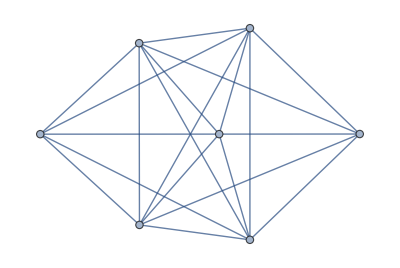
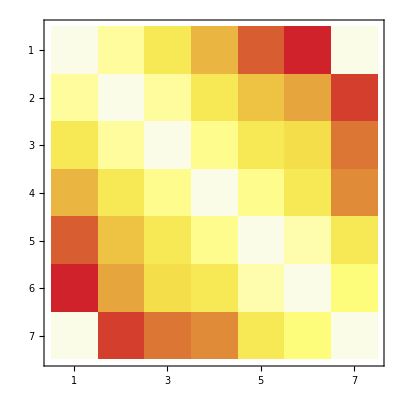
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
M=GenerateRandomDMDGPInstance[7];
X=M["X"]
{G=M["G"],MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"TemperatureMap"],MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"Monochrome"]}
```

```mathematica
AdjacencyList[G,1]
```

{2,3,4,5,6}

```mathematica
IncidenceMatrix[NeighborhoodGraph[G,1]]
```

SparseArray[<30>, {6, 15}]

```mathematica
e=EdgeList[G,1<->_]
```

{1<->2,1<->3,1<->4,1<->5,1<->6}

```mathematica
ss[x_]:=Module[{},x[[1]]=2];SetAttributes[ss,HoldFirst];
```

```mathematica
x={1,3}
```

{1,3}

```mathematica
AnyTrue[x,#>5&]
```

False

```mathematica
x=y=3
```

```mathematica
x
```

3

```mathematica
y
```

3